```mathematica
Integrate[Sin[θ1]*Sin[θ2]*Exp[-β*D1^2/(2*χ1)]*Exp[-β*D2^2/(2*χ2)]*(D1*D2)^2*(β^2/2)*(2*Cos[θ1]*Cos[θ2]-Sin[θ1]*Sin[θ2]*Cos[ϕ1-ϕ2])^2/r^6,{D1,0,Infinity},{D2,0,Infinity},{θ1,0,Pi},{θ2,0,Pi},{ϕ1,0,2*Pi},{ϕ2,0,2*Pi}]//FullSimplify
```

ConditionalExpression[(8 π^3 √(β/χ2) χ2^2)/(3 r^6 (β/χ1)^(3/2)), Re[β/χ1]>0]

```mathematica
Integrate[Sin[θ1]*Sin[θ2]*Exp[-β*D1^2/(2*χ1)]*Exp[-β*D2^2/(2*χ2)],{D1,0,Infinity},{D2,0,Infinity},{θ1,0,Pi},{θ2,0,Pi},{ϕ1,0,2*Pi},{ϕ2,0,2*Pi}]//FullSimplify
```

ConditionalExpression[(8 π^3 √(χ1 χ2))/β, Re[β]>0]

```mathematica
Series[Exp[-x],{x,0,4}]
```

1-x+x^2/2-x^3/6+x^4/24+O[x]^5

```mathematica
Integrate[Sin[θ1]*Sin[θ2]*β (D1*D2)/(R^3)*(2*Cos[θ1]*Cos[θ2]-Sin[θ1]*Sin[θ2]*Cos[ϕ1-ϕ2]),{θ1,0,Pi},{θ2,0,Pi},{ϕ1,0,2 Pi},{ϕ2,0,2 Pi}]
```

0

```mathematica
Integrate[Sin[θ1]*Sin[θ2]*(β^2/
	2)*(D1*D2)^2/(R^6)*(2*Cos[θ1]*Cos[θ2] - 
	Sin[θ1]*Sin[θ2]*
	Cos[ϕ1 - ϕ2] )^2, {θ1, 0, Pi}, {θ2, 0, 
	Pi}, {ϕ1, 0, 2 Pi}, {ϕ2, 0, 2 Pi}]
```

(16 D1^2 D2^2 π^2 β^2)/(3 R^6)

```mathematica
Integrate[d^2*Exp[-d/T]/T^2,{d,0,Delta}]
```

2 T-(ⅇ^(-Delta/T) (Delta^2+2 Delta T+2 T^2))/T

```mathematica
D[Integrate[d^2*Exp[-d/T]/T^2,{d,0,Delta}],T]//FullSimplify
```

2-(ⅇ^(-Delta/T) (Delta+T) (Delta^2+2 T^2))/T^3

General::munfl: Exp[-48951.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

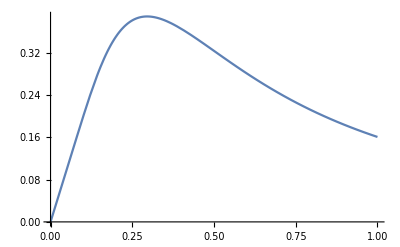

```mathematica
Plot[Integrate[d^2*Exp[-d/T]/T^2,{d,0,1}],{T,0,1}]
```

```mathematica
D[Integrate[d^2*Exp[d/T]/T^2,{d,0,Delta}],T]//FullSimplify
```

-2+(ⅇ^(Delta/T) (-Delta+T) (Delta^2+2 T^2))/T^3

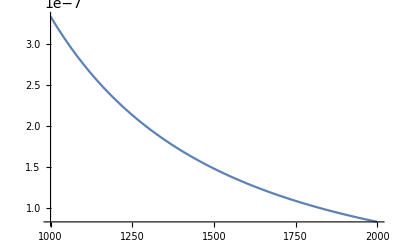

```mathematica
Plot[Integrate[d^2*Exp[d/T]/T^2,{d,0,1}],{T,1000,2000}]
```

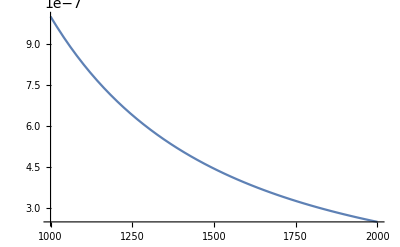

```mathematica
Plot[1/T^2,{T,1000,2000}]
```

```mathematica
Integrate[d^(n+2)*Exp[-d/T]/T^2,{d,0,Infinity}]//FullSimplify
```

ConditionalExpression[T^(1+n) Gamma[3+n], Re[n]>-3&&Re[T]>0]